```mathematica
(* VBP1 (Bartonella) PREVALENCE *)
```

```mathematica
(* Turn off Solve warning messages *)
Off[Solve::ratnz]

(* Function to generate table of mean burdens for ρ=0 and ρ=1, for all θ1 and θ2 combinations *)
provchange[pars_]:=
Module[{data},
data= Table[Table[Solve[system//.provpars//.pars,{prevv,prevh,nh,nv}][[5]],{prov,0,1}],{θ1,0,5},{θ2,0,5}];
Table[(prevh/.data[[i]][[j]][[2]])-(prevh/.data[[i]][[j]][[1]]),{i,1,6},{j,1,6}]
]

(* Provisioning response calculations *)
provpars={δp->δmin+(δmax-δmin)*E^(-θ1*prov),αp->αmax-(αmax-αmin)*E^(-θ2*prov)};

(* System equations *)
system={αp*ω*prevh*nh*(1-prevv)-bv*prevv*(kv-nv)/kv==0 && αp*δp*prevv*nv*(1-prevh)-(μh+ν+γ)*prevh-prevh*bh*(K-nh)/K+μh*prevh+ν*prevh^2==0 && bh*nh*(K-nh)/K-μh*nh-ν*prevh*nh==0&& bv*nv*(kv-nv)/kv-μv*nv==0};
```

```mathematica
(* GENERATE PLOTS VARYING BY K *)

(* Compile parameter lists *)
pars1={K->42.12,bh->1.24,δ->1,α->0.00815,γ->0.643,ν->0,δmax->0.815,δmin->δmax/2,αmin->1*^-2,αmax->2*^-2,λ->1,ω->50.6,bv->100,kv->K*2,ν->0,μh ->1/13.75, μv->1/4};
pars2={K->42.12*1.5,bh->1.24,δ->1,α->0.00815,γ->0.643,ν->0,δmax->0.815,δmin->δmax/2,αmin->1*^-2,αmax->2*^-2,λ->1,ω->50.6,bv->100,kv->K*2,ν->0,μh ->1/13.75, μv->1/4};
pars3={K->42.12*2,bh->1.24,δ->1,α->0.00815,γ->0.643,ν->0,δmax->0.815,δmin->δmax/2,αmin->1*^-2,αmax->2*^-2,λ->1,ω->50.6,bv->100,kv->K*2,ν->0,μh ->1/13.75, μv->1/4};

(* Generate tables of differences in predicted prevalences for all θ1 and θ2 combinations *)
resprevh1 =provchange[pars1]
resprevh2 =provchange[pars2]
resprevh3 =provchange[pars3]
```

{{0.,0.124046,0.155824,0.166253,0.169939,0.171276},{-0.0945772,0.0301671,0.0639915,0.0752717,0.0792803,0.0807367},{-0.138697,-0.0167294,0.0172615,0.0286892,0.0327614,0.0342423},{-0.156572,-0.0363364,-0.00244856,0.00898307,0.0130615,0.0145452},{-0.163396,-0.0439166,-0.0100961,0.00132771,0.00540517,0.00688881},{-0.165941,-0.0467577,-0.0129664,-0.00154686,0.00252976,0.00401319}}

{{0.,0.113346,0.140819,0.149701,0.152824,0.153955},{-0.0947818,0.02779,0.0591657,0.0694584,0.0730957,0.0744145},{-0.141572,-0.0173664,0.015331,0.0261408,0.0299709,0.0313608},{-0.161027,-0.0367544,-0.00364927,0.00733204,0.0112273,0.0126415},{-0.168531,-0.0443327,-0.0110945,-0.0000545719,0.00386319,0.00528577},{-0.171341,-0.0471851,-0.0139006,-0.00283992,0.00108588,0.00251147}}

{{0.,0.1019,0.125719,0.133348,0.136023,0.13699},{-0.0904691,0.0252712,0.0537246,0.0629572,0.0662081,0.0673852},{-0.136949,-0.0166462,0.013735,0.023664,0.0271684,0.0284384},{-0.156644,-0.0349691,-0.00388245,0.00630911,0.00990994,0.0112154},{-0.164301,-0.0421852,-0.0108439,-0.000556111,0.00308024,0.00439877},{-0.167176,-0.0449093,-0.0134752,-0.00315216,0.000497227,0.00182056}}

-0.2

0.2

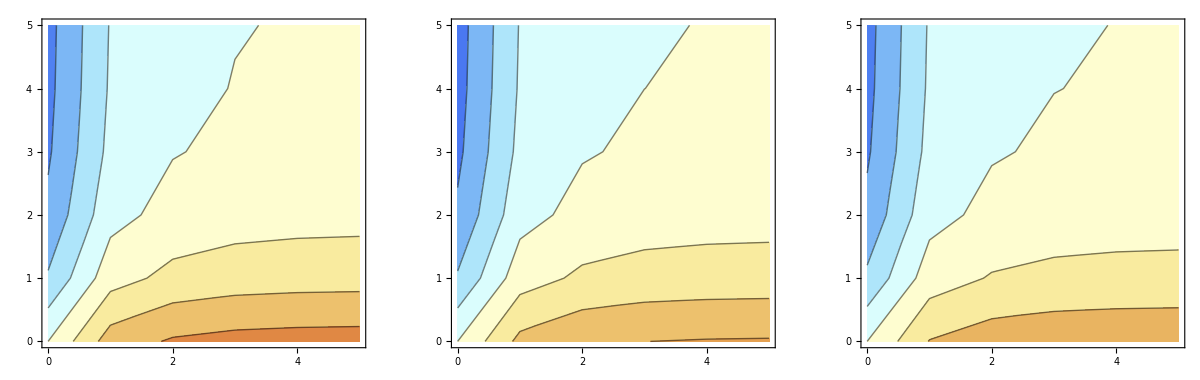

```mathematica
(* Calculate min and max values across all resprevh arrays, rounding up/down to nearest value to 1 decimal place *)
(* Note, these scale within the above 3 generated plots; to scale across all parasites would need to calculate min and maxvals across them all *)
minvals=Floor[Min[resprevh1,resprevh2,resprevh3]*10]/10//N
maxvals=Ceiling[Max[resprevh1,resprevh2,resprevh3]*10]/10//N

(* Now create all 3 graphs, using the same common min and max values *)
p1=ListContourPlot[resprevh1,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
p2=ListContourPlot[resprevh2,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
p3=ListContourPlot[resprevh3,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
Show[GraphicsGrid[{{p1,p2,p3}}]]

(* Create a legend spanning specified range (minvals to maxvals) *)
BarLegend[{"LightTemperatureMap",{minvals,maxvals}}]
```

```mathematica
(* GENERATE PLOTS VARYING BY b *)

(* Compile parameter lists *)
pars1={K->42.12,bh->1.24,δ->1,α->0.00815,γ->0.643,ν->0,δmax->0.815,δmin->δmax/2,αmin->1*^-2,αmax->2*^-2,λ->1,ω->50.6,bv->100,kv->K*2,ν->0,μh ->1/13.75, μv->1/4};
pars2={K->42.12,bh->1.24*1.5,δ->1,α->0.00815,γ->0.643,ν->0,δmax->0.815,δmin->δmax/2,αmin->1*^-2,αmax->2*^-2,λ->1,ω->50.6,bv->100,kv->K*2,ν->0,μh ->1/13.75, μv->1/4};
pars3={K->42.12,bh->1.24*2,δ->1,α->0.00815,γ->0.643,ν->0,δmax->0.815,δmin->δmax/2,αmin->1*^-2,αmax->2*^-2,λ->1,ω->50.6,bv->100,kv->K*2,ν->0,μh ->1/13.75, μv->1/4};

(* Generate tables of differences in predicted prevalences for all θ1 and θ2 combinations *)
resprevh1 =provchange[pars1]
resprevh2 =provchange[pars2]
resprevh3 =provchange[pars3]
```

{{0.,0.124046,0.155824,0.166253,0.169939,0.171276},{-0.0945772,0.0301671,0.0639915,0.0752717,0.0792803,0.0807367},{-0.138697,-0.0167294,0.0172615,0.0286892,0.0327614,0.0342423},{-0.156572,-0.0363364,-0.00244856,0.00898307,0.0130615,0.0145452},{-0.163396,-0.0439166,-0.0100961,0.00132771,0.00540517,0.00688881},{-0.165941,-0.0467577,-0.0129664,-0.00154686,0.00252976,0.00401319}}

{{0.,0.123977,0.155743,0.166169,0.169854,0.17119},{-0.0945535,0.0301126,0.0639231,0.0751993,0.0792065,0.0806623},{-0.138662,-0.0167766,0.0171995,0.0286227,0.0326935,0.0341738},{-0.156533,-0.0363806,-0.00250791,0.00891918,0.012996,0.0144792},{-0.163355,-0.0439596,-0.0101544,0.00126482,0.0053407,0.00682378},{-0.165899,-0.0468003,-0.0130244,-0.00160939,0.00246566,0.00394852}}

{{0.,0.123944,0.155704,0.166128,0.169812,0.171148},{-0.094542,0.0300862,0.06389,0.0751641,0.0791707,0.0806262},{-0.138646,-0.0167995,0.0171694,0.0285905,0.0326605,0.0341406},{-0.156514,-0.036402,-0.00253669,0.0088882,0.0129643,0.0144472},{-0.163335,-0.0439805,-0.0101827,0.00123432,0.00530944,0.00679225},{-0.165879,-0.0468209,-0.0130525,-0.00163971,0.00243457,0.00391716}}

-0.2

0.2

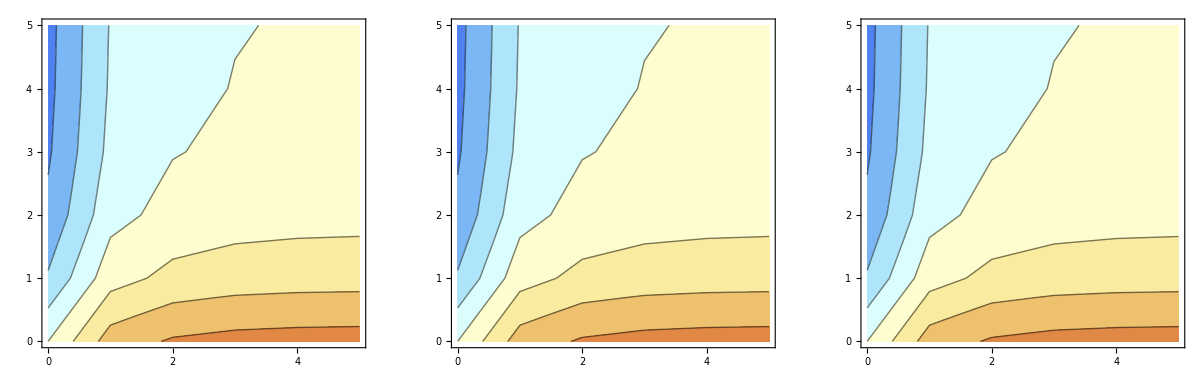

```mathematica
(* Calculate min and max values across all resprevh arrays, rounding up/down to nearest value to 1 decimal place *)
(* Note, these scale within the above 3 generated plots; to scale across all parasites would need to calculate min and maxvals across them all *)
minvals=Floor[Min[resprevh1,resprevh2,resprevh3]*10]/10//N
maxvals=Ceiling[Max[resprevh1,resprevh2,resprevh3]*10]/10//N

(* Now create all 3 graphs, using the same common min and max values *)
p1=ListContourPlot[resprevh1,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
p2=ListContourPlot[resprevh2,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
p3=ListContourPlot[resprevh3,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
Show[GraphicsGrid[{{p1,p2,p3}}]]

(* Create a legend spanning specified range (minvals to maxvals) *)
BarLegend[{"LightTemperatureMap",{minvals,maxvals}}]
```

```mathematica
(* GENERATE PLOTS VARYING BY μ *)

(* Compile parameter lists *)
pars1={K->42.12,bh->1.24,δ->1,α->0.00815,γ->0.643,ν->0,δmax->0.815,δmin->δmax/2,αmin->1*^-2,αmax->2*^-2,λ->1,ω->50.6,bv->100,kv->K*2,ν->0,μh ->1/13.75, μv->1/4};
pars2={K->42.12,bh->1.24,δ->1,α->0.00815,γ->0.643,ν->0,δmax->0.815,δmin->δmax/2,αmin->1*^-2,αmax->2*^-2,λ->1,ω->50.6,bv->100,kv->K*2,ν->0,μh ->1/13.75/1.5, μv->1/4};
pars3={K->42.12,bh->1.24,δ->1,α->0.00815,γ->0.643,ν->0,δmax->0.815,δmin->δmax/2,αmin->1*^-2,αmax->2*^-2,λ->1,ω->50.6,bv->100,kv->K*2,ν->0,μh ->1/13.75/2, μv->1/4};

(* Generate tables of differences in predicted prevalences for all θ1 and θ2 combinations *)
resprevh1 =provchange[pars1]
resprevh2 =provchange[pars2]
resprevh3 =provchange[pars3]
```

{{0.,0.124046,0.155824,0.166253,0.169939,0.171276},{-0.0945772,0.0301671,0.0639915,0.0752717,0.0792803,0.0807367},{-0.138697,-0.0167294,0.0172615,0.0286892,0.0327614,0.0342423},{-0.156572,-0.0363364,-0.00244856,0.00898307,0.0130615,0.0145452},{-0.163396,-0.0439166,-0.0100961,0.00132771,0.00540517,0.00688881},{-0.165941,-0.0467577,-0.0129664,-0.00154686,0.00252976,0.00401319}}

{{0.,0.123489,0.154969,0.165286,0.168931,0.170253},{-0.0949029,0.0300585,0.0637753,0.0750035,0.0789916,0.0804402},{-0.139385,-0.0168388,0.0171504,0.028561,0.0326251,0.0341028},{-0.157445,-0.0364909,-0.00256017,0.00886949,0.0129452,0.0144277},{-0.164344,-0.0440956,-0.0102151,0.00121266,0.00528949,0.00677264},{-0.166919,-0.0469468,-0.0130892,-0.00166351,0.00241327,0.00389649}}

{{0.,0.12318,0.154501,0.16476,0.168383,0.169696},{-0.0950496,0.0299986,0.0636532,0.0748523,0.0788292,0.0802735},{-0.139709,-0.0168886,0.0170925,0.0284919,0.032551,0.0340268},{-0.157861,-0.0365594,-0.00261378,0.00881243,0.0128858,0.0143674},{-0.164799,-0.044175,-0.0102707,0.00115658,0.00523221,0.00671479},{-0.167388,-0.0470308,-0.0131461,-0.00171976,0.00235623,0.00383903}}

-0.2

0.2

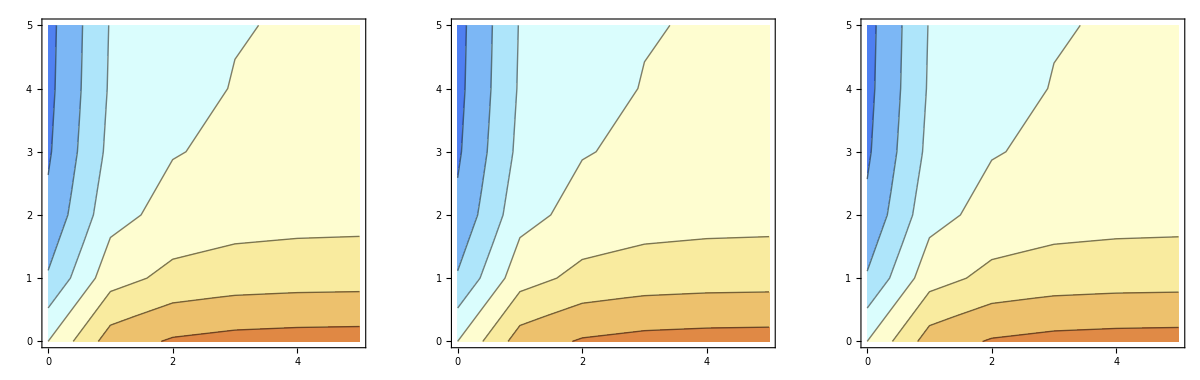

```mathematica
(* Calculate min and max values across all resprevh arrays, rounding up/down to nearest value to 1 decimal place *)
(* Note, these scale within the above 3 generated plots; to scale across all parasites would need to calculate min and maxvals across them all *)
minvals=Floor[Min[resprevh1,resprevh2,resprevh3]*10]/10//N
maxvals=Ceiling[Max[resprevh1,resprevh2,resprevh3]*10]/10//N

(* Now create all 3 graphs, using the same common min and max values *)
p1=ListContourPlot[resprevh1,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
p2=ListContourPlot[resprevh2,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
p3=ListContourPlot[resprevh3,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
Show[GraphicsGrid[{{p1,p2,p3}}]]

(* Create a legend spanning specified range (minvals to maxvals) *)
BarLegend[{"LightTemperatureMap",{minvals,maxvals}}]
```